```mathematica
(* Human parameters *)
n=8 10^6;
γ=1./14.;

(* Mosquito parameters *) 
m=7.5*n;
μ=0.0476190476190476;
a=0.12;

(* Infectivity parameters *)
Subscript[β, vh]=0.5;
Subscript[β, hv]=0.1;
τ=10;

(* Control parameters *)
κ=0.44;
u=0.15;

b=Subscript[β, vh](E^(-μ τ)a m)/n;
c=Subscript[β, hv] a;

Imax=0.1;

equilibrium = {x,y}/.NSolve[
(1-x)(1-κ u)b y - γ x==0&&
(1-y)(1-κ u)c x - μ y==0&&
x>=0&&y>=0&&
x≤1&&y≤1,
{x,y},Reals]⟦1⟧
equilibrium⟦1⟧<=Imax
```

{0.,0.}

True

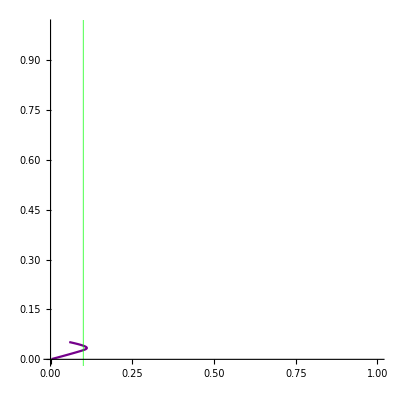

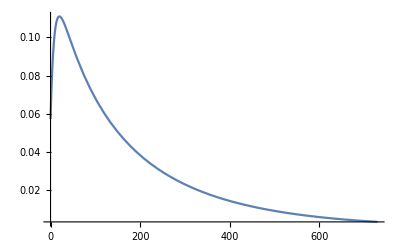

patch-dynamics-disjoint-1-2.csv

{0.00339029,0.000875439}

```mathematica
{x0,y0}={0.05720000,0.05200000};
tMax=730;
numericalIntegration =NDSolve[{
x'[t]==(1-x[t])(1-κ u)b y[t] - γ x[t],
y'[t]==(1-y[t])(1-κ u)c x[t] - μ y[t],
x[0]==x0,y[0]==y0},
{x,y},
{t,0,tMax}
];
{humans,mosquitos}={x,y}/.numericalIntegration⟦1⟧;
solutionPlot=ParametricPlot[{humans[t],mosquitos[t]},{t,0,tMax},PlotRange->{{0,1},{0,1}},GridLines->{{Imax},{2}},GridLinesStyle->Directive[Green,Thick],ColorFunction->Function[{x,y,tscaled},Blend[{Red,Blue},Power[tscaled, 0.3]]]];
Show[{solutionPlot}]
Plot[humans[t],{t,0,tMax},PlotRange->All]
humanSolution = (<|"t"->#⟦1⟧,"x1"->#⟦2⟧|>)&/@Table[{t,humans[t]},{t,0,tMax}] //Dataset;
SetDirectory[NotebookDirectory[]];
Export["patch-dynamics-disjoint-1-2.csv",humanSolution]
{humans[tMax], mosquitos[tMax]}
```

```mathematica
humanSolutions = ({#⟦1⟧,#⟦2⟧,{Subscript[x, 1],Subscript[x, 2]}/.(#⟦3⟧⟦1⟧)}&)/@equilibriumPoints;
botswanaNormalized = ({#⟦1⟧,#⟦2⟧,#⟦3⟧⟦1⟧}&)/@humanSolutions;
zimbabweNormalized = ({#⟦1⟧,#⟦2⟧,#⟦3⟧⟦2⟧}&)/@humanSolutions;
```

```mathematica
(* YES 0.05000000,0.00833333,0.06875000,0.06875000,  *)
(* YES 0.05000000,0.04375000,0.07083333,0.02083333, -8.15115601e-08 *)
(* NO 0.05000000,0.04375000,0.06666667,0.09583333, -7.15743167e-08 *)
(* NO 0.08125000,0.10625000,0.05000000,0.07500000, -5.43740266e-08 *)
(* YES 0.14375000,0.01250000,-0.00833333,0.00000000, -8.44697592e-08 *)
(* NO 0.10625000,0.13750000,0.11666667,0.05000000, -4.75063590e-10 *)
(* YES 0.06875000,0.04375000,0.05416667,0.02916667, -7.70061768e-10 *)
(* NO 0.06875000,0.04375000,0.05416667,0.09583333, -6.85949469e-10 *)
```